## The solution will be X=Exp[I m φ]/Sqrt[x] {X1,Exp[I φ]X2,Exp[I φ]X3,Exp[2 I φ]X4,Exp[2 I φ]X5,Exp[3 I φ]X6} x=ξ=r/Sqrt[2]/lB j=m+1/2

```mathematica
Dd[j_,x_,f_]:=D[f,x]+(j-1)/x f+x f
Du[j_,x_,f_]:=D[f,x]-(j-1)/x f-x f
```

## Sol1

```mathematica
X1=Exp[-x^2/2]x^((m+1/2))LaguerreL[-(m+1/2)-1/2+n,(m+1/2)-1/2,x^2]
X2=Exp[-x^2/2]x^((m+1/2)+1)LaguerreL[-(m+1/2)-1/2+n,(m+1/2)+1/2,x^2]
X3=X2
X4=Exp[-x^2/2]x^((m+1/2)+2)LaguerreL[-(m+1/2)-1/2+n,(m+1/2)+3/2,x^2]
X5=X4
X6=Exp[-x^2/2]x^((m+1/2)+3)LaguerreL[-(m+1/2)-1/2+n,(m+1/2)+5/2,x^2]
```

ⅇ^(-x^2/2) x^(1/2+m) LaguerreL[-1-m+n,m,x^2]

ⅇ^(-x^2/2) x^(3/2+m) LaguerreL[-1-m+n,1+m,x^2]

ⅇ^(-x^2/2) x^(3/2+m) LaguerreL[-1-m+n,1+m,x^2]

ⅇ^(-x^2/2) x^(5/2+m) LaguerreL[-1-m+n,2+m,x^2]

ⅇ^(-x^2/2) x^(5/2+m) LaguerreL[-1-m+n,2+m,x^2]

ⅇ^(-x^2/2) x^(7/2+m) LaguerreL[-1-m+n,3+m,x^2]

```mathematica
"Du[(m+1/2)+1,x,X1]/X2=-2
Dd[(m+1/2)+1,x,X2]/X1=2n
Du[(m+1/2)+2,x,X3]/X4=-2
Dd[(m+1/2)+2,x,X4]/X3=2n+2
Du[(m+1/2)+3,x,X5]/X6=-2
Dd[(m+1/2)+3,x,X6]/X5=2n+4"
```

## Sol2

```mathematica
Clear[k]
X1=Exp[-x^2/2]x^(-(m+1/2)+1)LaguerreL[-1+n,-(m+1/2)+1/2,x^2];
X2=Exp[-x^2/2]x^(-(m+1/2))LaguerreL[n,-(m+1/2)-1/2,x^2];
X3=X2;
X4=Exp[-x^2/2]x^(-(m+1/2)-1)LaguerreL[1+n,-(m+1/2)-3/2,x^2];
X5=X4;
X6=Exp[-x^2/2]x^(-(m+1/2)-2)LaguerreL[2+n,-(m+1/2)-5/2,x^2];
```

```mathematica
"Du[(m+1/2)+1,x,X1]/X2=2n
Dd[(m+1/2)+1,x,X2]/X1=-2
Du[(m+1/2)+2,x,X3]/X4=2n+2
Dd[(m+1/2)+2,x,X4]/X3=-2
Du[(m+1/2)+3,x,X5]/X6=2n+4
Dd[(m+1/2)+3,x,X6]/X5=-2"
```

## Landau Level expression

```mathematica
b2=-2;
b1=2 n;
b4=-2;
b3=2 n+2;
b6=-2;
b5=2 n+4;
Cp=-I/Sqrt[2]/lB;
Hr=SparseArray[{Band[{2,1}]->Cp{b2,0,b4,0,b6},Band[{1,2}]->Cp{b1,0,b3,0,b5}},{6,6}]+SparseArray[{Band[{1,2}]->{0,γeV,0,γeV,0},Band[{2,1}]-> {0,γeV,0,γeV,0}},{6,6}];
Hr//MatrixForm
ΔB=Sqrt[2]vF/lB;
Hxy=SparseArray[{Band[{2,1}]->ΔB{Sqrt[n],0,Sqrt[n+1],0,Sqrt[n+2]},Band[{1,2}]->ΔB{Sqrt[n],0,Sqrt[n+1],0,Sqrt[n+2]}},{6,6}]+SparseArray[{Band[{1,2}]->{0,γeV,0,γeV,0},Band[{2,1}]-> {0,γeV,0,γeV,0}},{6,6}];
Hxy//MatrixForm
```

(0 | -(ⅈ √2 n)/lB | 0 | 0 | 0 | 0
(ⅈ √2)/lB | 0 | γeV | 0 | 0 | 0
0 | γeV | 0 | -(ⅈ (2+2 n))/(√2 lB) | 0 | 0
0 | 0 | (ⅈ √2)/lB | 0 | γeV | 0
0 | 0 | 0 | γeV | 0 | -(ⅈ (4+2 n))/(√2 lB)
0 | 0 | 0 | 0 | (ⅈ √2)/lB | 0)

(0 | (√2 √n vF)/lB | 0 | 0 | 0 | 0
(√2 √n vF)/lB | 0 | γeV | 0 | 0 | 0
0 | γeV | 0 | (√2 √(1+n) vF)/lB | 0 | 0
0 | 0 | (√2 √(1+n) vF)/lB | 0 | γeV | 0
0 | 0 | 0 | γeV | 0 | (√2 √(2+n) vF)/lB
0 | 0 | 0 | 0 | (√2 √(2+n) vF)/lB | 0)

```mathematica
Eigenvalues[Hr]-Eigenvalues[Hxy]/.{lB->1,vF->1}
```

{0,0,0,0,0,0}

```mathematica
e=1.6 10^-19;
ℏ=6.63 10^-34;
lB=N[Sqrt[ℏ/e/B],∞];
fx=Exp[-x^2/2]x^((m+1/2)+1)LaguerreL[-(m+1/2)-1/2+n,(m+1/2)+1/2,x^2];
Manipulate[Plot[Exp[-x^2/2]x^((m+1/2)+1)LaguerreL[-(m+1/2)-1/2+n,(m+1/2)+1/2,x^2],{x,0,10},PlotRange->All,WorkingPrecision->100,AxesStyle->{20,10}],{n,0,50,1},{{m,-1},-50,50,1}]
```

```mathematica
Manipulate[
FMaxSol=FindMaximum[Abs[Exp[-x^2/2]x^((m+1/2)+1)LaguerreL[-(m+1/2)-1/2+n,(m+1/2)+1/2,x^2]],x,WorkingPrecision->40];{N[FMaxSol[[1]]/10,4],N[FindRoot[FMaxSol[[1]]/10==Abs[Exp[-x^2/2]x^((m+1/2)+1)LaguerreL[-(m+1/2)-1/2+n,(m+1/2)+1/2,x^2]],{x,(x/.FMaxSol[[2]])+{-1,1}},WorkingPrecision->40],4],Plot[{FMaxSol[[1]]/10,Exp[-x^2/2]x^((m+1/2)+1)LaguerreL[-(m+1/2)-1/2+n,(m+1/2)+1/2,x^2]},{x,0,10},PlotRange->All,WorkingPrecision->40,AxesStyle->{20,10}]},{{n,0},0,50,1},{{m,-1},-50,50,1}]
```

```mathematica
WP=1000;
edge=ParallelTable[FMaxSol=FindMaximum[Abs[Exp[-x^2/2]x^((m+1/2)+1)LaguerreL[-(m+1/2)-1/2+n,(m+1/2)+1/2,x^2]/.n->0],x,WorkingPrecision->WP];x/.FindRoot[FMaxSol[[1]]/10==Abs[Exp[-x^2/2]x^((m+1/2)+1)LaguerreL[-(m+1/2)-1/2+n,(m+1/2)+1/2,x^2]/.n->0],{x,(x/.FMaxSol[[2]])+{-1,1}},WorkingPrecision->WP],{m,-1,-100,-1}];
```

{a→-1.703,b→1.028,c→1.482}

{a→1.555,b→0.9948,c→-0.03018}

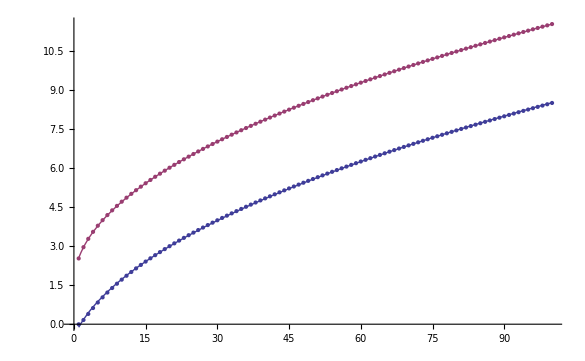

```mathematica
fit1=N[FindFit[edge[[All,1]],a+Sqrt[b x+c],{a,b,c},x,MaxIterations->500],4]
fit2=N[FindFit[edge[[All,2]],a+Sqrt[b x+c],{a,b,c},x,MaxIterations->500],4]
Show[{ListPlot[{edge[[All,1]],edge[[All,2]]},PlotStyle->PointSize[Medium]],Plot[{(a+Sqrt[b x+c])/.fit1,(a+Sqrt[b x+c])/.fit2},{x,1,100}]}]
```

```mathematica
Bu2
```

2.954

```mathematica
Bl10=((a+Sqrt[b Abs[m]+c])/.fit1/.m->10);
Bu10=((a+Sqrt[b Abs[m]+c])/.fit2/.m->10);
Bl2=((a+Sqrt[b Abs[m]+c])/.fit1/.m->2);
Bu2=((a+Sqrt[b Abs[m]+c])/.fit2/.m->2);
Bl100=((a+Sqrt[b Abs[m]+c])/.fit1/.m->100);
Bu100=((a+Sqrt[b Abs[m]+c])/.fit2/.m->100);
R=SetPrecision[200*10^-9,∞];
e=1.6 10^-19;
ℏ=6.63 10^-34;
lB=SetPrecision[Sqrt[ℏ/e/B],∞];
```

```mathematica
lB
```

(4863808230862035 √(1/B))/75557863725914323419136

```mathematica
"hybridization range for n=0 m=-10:"N[Reduce[SetPrecision[Bl10<R /Sqrt[2]/lB<Bu10,∞],B],3]
"hybridization range for n=0 m=-2:"Reduce[Bl2<R /Sqrt[2]/lB<Bu2,B]
"hybridization range for n=0 m=-100:"Reduce[Bl100<R /Sqrt[2]/lB<Bu100,B]
```

hybridization range for n=0 m=-10: (0.618<B<4.58)

Reduce::ratnz: Reduce 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

hybridization range for n=0 m=-2: (0.006582626557789434<B<1.80850408058165)

Reduce::ratnz: Reduce 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

hybridization range for n=0 m=-100: (15.00256541951044<B<27.52920164071335)